```mathematica
ClearAll["Global`*"]
```

```mathematica
path="/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/";
file[name_]:=StringJoin[path,name];
read[name_]:=Flatten[Import[name,"Table"]];
```

```mathematica
files=FileNames["*.bin",NotebookDirectory[]];
Do[Print[files[[i]]],{i,1,Length[files]}]
```

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/ENER.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/ENER-Ge-BM.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE-Ge-BM.bin

```mathematica
energyExp=read[files[[1]]];
energyTh=read[files[[2]]];
strengthEx=read[files[[3]]];
strengthTh=read[files[[4]]];
makedata[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
isotope=Row[{Superscript["","76"],"Ge"}];
```

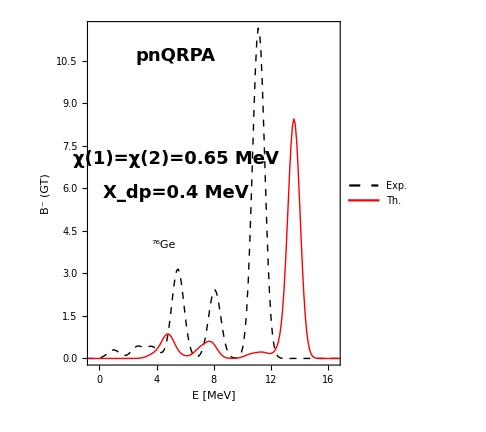

```mathematica
fig1=ListPlot[{makedata[energyExp,strengthEx],makedata[energyTh,strengthTh]},Joined->True,ImageSize->Medium,AspectRatio->1.2,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp.","Th."},{0.35,0.77}],Epilog->{Inset[Style["pnQRPA",18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.9}]],Inset[Style["χ(1)=χ(2)=0.65 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.6}]],Inset[Style["X_dp=0.4 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.5}]],Inset[Framed[Style[isotope,20,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.35}]]},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},PlotRange->{{-0.5,16.5},Full}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE-Ge-BM.pdf",Show[fig1],ImageResolution->1200];
```